## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[23]
```

{23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Topic

### Definition / Theorem

### This is text.

### Example

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,11}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -1/2
5 | 1/2
6 | -1/3
7 | 1/3
8 | -2
9 | 2
10 | -1/5
11 | 1/5

```mathematica
Table[{k,nNaturalToInteger[k]},{k,1,11}]//tf
Table[{k,nIntegerToNatural[k]},{k,-5,5}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -2
5 | 2
6 | -3
7 | 3
8 | -4
9 | 4
10 | -5
11 | 5

-5 | 10
-4 | 8
-3 | 6
-2 | 4
-1 | 2
0 | 1
1 | 3
2 | 5
3 | 7
4 | 9
5 | 11

```mathematica
nNaturalToQuotient[101]
```

5/2

```mathematica
nNaturalToInteger[25]
```

12

```mathematica
FactorInteger[1251]
```

{{3,2},{139,1}}

## Framework for Sets

Here is one idea. Convert the set expression into an equivalent boolean expression, use BooleanMinimize to simplify the boolean expression, and then convert back to a set expression.

Set expression

Rather than using Union and Intersection, I will use the built-in symbols SquareUnion and SquareIntersection so that I don’t have to modify Union and Intersection to work with atomic symbols. So, here are the symbols I will be allowing for set expressions:

union: SquareUnion (A⊔B)
intersection: SquareIntersection (A⊓B)
subset: SquareSubset (A⊏B)
superset: SquareSuperset (A⊐B)
set difference: Backslash (A∖B)
set complement: OverBar (A.af)
set equivalence: Equal
empty set: EmptySet (∅)
universal set: UniversalSet (U)

Check the following code with the code above... then Choose how to implement.

```mathematica
MakeBoxes[EmptySet,form_]^=TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)];
MakeBoxes[UniversalSet,form_]^=TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)];

CurrentValue[EvaluationNotebook[],InputAliases]={"su"->"⊔","si"->"⊓","sb"->"⊏","sp"->"⊐","es"->TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)],"us"->TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)]};

toBoolean[expr_]:=ReplaceAll[expr,{SquareUnion->Or,SquareIntersection->And,SquareSubset->Implies,SquareSuperset->Reverse@*Implies,OverBar->Not,Backslash->(And[#1,!#2]&),Equal->Equivalent,EmptySet->False,UniversalSet->True}]

setQ[EmptySet]=True;
setQ[UniversalSet]=True;
setQ[_Symbol]=True;

setQ[(Backslash|SquareUnion|SquareIntersection|OverBar)[a__]]:=AllTrue[{a},setQ]

setQ[_]=False;

fromBoolean[expr_]:=ReplaceAll[expr,{Or->SquareUnion,And->SquareIntersection,Not->OverBar,Equivalent->Equal}]
fromBoolean[a_&&!b_Symbol]:=Backslash[a,b]
fromBoolean[!a_Symbol&&b_]:=Backslash[b,a]
fromBoolean[a_||!b_Symbol]:=SquareSubset[b,a]
fromBoolean[!a_Symbol||b_]:=SquareSubset[a,b]

Options[SetSimplify]={Method->Automatic};

SetSimplify[set_,cond_:True,OptionsPattern[]]:=Module[{res},res=fromBoolean@BooleanMinimize[toBoolean[set],toBoolean[cond],Method->OptionValue[Method]];
If[setQ[set],res/. {False->EmptySet,True->UniversalSet},res]]
```

## Axioms of R

### Field Axioms

### Order Axioms

### Completeness Axioms

## Tmp-1

```mathematica
DirichletBeta[1]
```

π/4

```mathematica
Piecewise
```

```mathematica
f[x_]:=Piecewise[{{1,x^2<2},{0,x^2>=2}}]
```

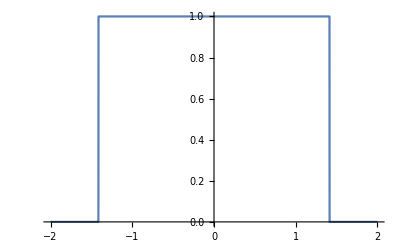

```mathematica
Plot[f[x],{x,-2,2}]
```

## Tmp-2

```mathematica
nz[n_] := (-1)^(n - 1) Floor[n/2]

zn[n_] := Piecewise[{{2 Abs[n], n < 0}, {2 n + 1, n > 0}, {1, n == 0}}]

zq1[n_] := 
 Piecewise[{{Apply[Times, 
     Map[#[[1]]^nz[#[[2]] + 1] &, FactorInteger[n]]], n != 0}, {0, 
    n == 0}}]

zq[n_] := Piecewise[{{zq1[n], n > 0}, {-zq1[-n], n < 0}, {0, n == 0}}]

qz[n_] := Piecewise[{{qz1[n], n > 0}, {-qz1[-n], n < 0}, {0, n == 0}}]

qz1[n_] := 
 Piecewise[{{Apply[Times, 
     Map[#[[1]]^(zn[#[[2]]] - 1) &, FactorInteger[n]]], n != 0}, {0, 
    n == 0}}]
```

## URM

```mathematica
t[m_,n_]:=Module[{},
l=ReplacePart[l,n->l[[m]]];
l]

s[n_]:=Module[
{},
l=ReplacePart[l,n->l[[n]]+1];
l]

z[n_]:=Module[
{},
l=ReplacePart[l,n->0];l]
```

```mathematica
l:=Array[0#&,10]

held=Hold[s[5],s[5],s[5],s[5],t[5,1],t[5,2],t[5,6],t[5,10]];
exec[n_]:=MapAt[Evaluate,held,n]

exec[1];exec[7];
l
```

{0,0,0,0,1,1,0,0,0,0}

```mathematica
l:=Array[0#&,10];
l;
held1=Hold[s[5],s[6],s[7]];
held1=ReplacePart[held1,1->s[8]];
held1[[3]];
held1[[1]];
l
```

{0,0,0,0,0,0,1,1,0,0}

```mathematica
held1
```

Hold[{0,0,0,0,0,0,0,0,0,0},s[6],s[7]]

```mathematica
l
```

{0,0,0,0,0,0,1,1,0,0}

```mathematica
t[8,1]
t[1,2]
```

{1,0,0,0,0,0,1,1,0,0}

{1,1,0,0,0,0,1,1,0,0}

```mathematica
(* Idea : Join *)

ls1=Hold[s[5]]
ls2=Hold[s[6]]
ls3=Hold[s[7]]
```

Hold[s[5]]

Hold[s[6]]

Hold[s[7]]

```mathematica
lsa=Join[ls1,ls2]
```

Hold[s[5],s[6]]

```mathematica
lsa=Join[lsa,ls3]
```

Hold[s[5],s[6],s[7]]

```mathematica
l:=Array[0#&,10];
l
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
lsa[[2]]
lsa[[2]]
```

{0,0,0,0,0,2,0,0,0,0}

{0,0,0,0,0,3,0,0,0,0}

```mathematica
(* 
Next Task: List of s,z,t,j's : Hold/Join them.

 s[4],s[5],s[6]

	Wellicht moeten de s,z,t,j's vooraf al op Hold gezet worden ???
*)
```

## URM-2

```mathematica
t[m_,n_]:=Hold[Module[{},
l=ReplacePart[l,n->l[[m]]];
l]]

s[n_]:=Hold[Module[
{},
l=ReplacePart[l,n->l[[n]]+1];
l]]

z[n_]:=Hold[Module[
{},
l=ReplacePart[l,n->0];l]]

j[m_,n_,q_]:=Hold[Module[{},
If[l[[m]]==l[[n]],pcnt=q-1]];
]

exec[]:=Module[{},While[pcnt<=Length[p],p[[pcnt]];pcnt=pcnt+1];l];
```

```mathematica
l:=Array[0#&,10]
```

```mathematica
(* FIX: GitHub Authorization ISSUE =Brrr! *)


l:=Array[0#&,10]
l=ReplacePart[l,1->7];
l=ReplacePart[l,2->3];
p:=j[2,3,5]; 
p=Join[p,s[1]];
p=Join[p,s[3]];
p=Join[p,j[1,1,1]]; 
pcnt:=1
exec[]
```

{10,3,3,0,0,0,0,0,0,0}